# xlr8r-example

```mathematica
<<xlr8r.m
```

xlr8r 0.60 (15-Oct-2007) loaded 15-October-2007 14:04:11.361775 using Mathematica 6.0 for Mac OS X x86 (32-bit) (June 19, 2007)

## elementary mass-action reactions

```mathematica
interpret[{{A->B}}]
```

{{A'[t]==-A[t],B'[t]==A[t]},{A,B}}

```mathematica
interpret[{{A-> B,k}}]
```

{{A'[t]==-k A[t],B'[t]==k A[t]},{A,B}}

```mathematica
interpret[{{A1-> B,k1}, {A2-> B,k2}}]
```

{{A1'[t]==-k1 A1[t],A2'[t]==-k2 A2[t],B'[t]==k1 A1[t]+k2 A2[t]},{A1,A2,B}}

## Enzymatic Reaction

```mathematica
version1={{S+Enz-> X, a}, {X-> S+Enz,d}, {X-> P+Enz,k}};
version2={{Overscript[S⇄P, Enz],a,d,k}};
```

```mathematica
eqs1=interpret[version1]
```

{{Enz'[t]==-a Enz[t] S[t]+d X[t]+k X[t],P'[t]==k X[t],S'[t]==-a Enz[t] S[t]+d X[t],X'[t]==a Enz[t] S[t]-d X[t]-k X[t]},{Enz,P,S,X}}

```mathematica
eqs2=interpret[version2]
```

{{Enz'[t]==-a Enz[t] S[t]+d Bind[Enz,S][t]+k Bind[Enz,S][t],P'[t]==k Bind[Enz,S][t],S'[t]==-a Enz[t] S[t]+d Bind[Enz,S][t],Bind[Enz,S]'[t]==a Enz[t] S[t]-d Bind[Enz,S][t]-k Bind[Enz,S][t]},{Enz,P,S,Bind[Enz,S]}}

Observe that the two sets of equations are the same, with "X" replaced by "Bind[Enz,S]"

```mathematica
Print[eqs1[[1]]//TableForm];
Print[eqs2[[1]]//TableForm];
```

Enz'[t]==-a Enz[t] S[t]+d X[t]+k X[t]
P'[t]==k X[t]
S'[t]==-a Enz[t] S[t]+d X[t]
X'[t]==a Enz[t] S[t]-d X[t]-k X[t]

Enz'[t]==-a Enz[t] S[t]+d Bind[Enz,S][t]+k Bind[Enz,S][t]
P'[t]==k Bind[Enz,S][t]
S'[t]==-a Enz[t] S[t]+d Bind[Enz,S][t]
Bind[Enz,S]'[t]==a Enz[t] S[t]-d Bind[Enz,S][t]-k Bind[Enz,S][t]

```mathematica
myrates={k-> 2,d-> 1, a->3};
```

```mathematica
interpret[version1/.myrates]
```

{{Enz'[t]==-3 Enz[t] S[t]+3 X[t],P'[t]==2 X[t],S'[t]==-3 Enz[t] S[t]+X[t],X'[t]==3 Enz[t] S[t]-3 X[t]},{Enz,P,S,X}}

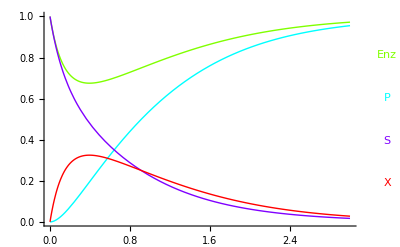

{{Enz→InterpolatingFunction[{{0.,3.}},<>],P→InterpolatingFunction[{{0.,3.}},<>],S→InterpolatingFunction[{{0.,3.}},<>],X→InterpolatingFunction[{{0.,3.}},<>]}}

```mathematica
run[version1, {0,3},rates-> myrates, initialConditions-> {Enz-> 1, S-> 1, P-> 0, X-> 0}, debug-> True, plot-> True]
```

Warning: Initial conditions are missing (and assumed to be zero) for the following variables: {Bind[Enz,S]}

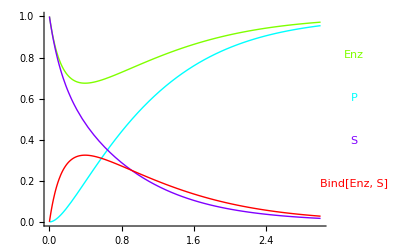

{{Enz→InterpolatingFunction[{{0.,3.}},<>],P→InterpolatingFunction[{{0.,3.}},<>],S→InterpolatingFunction[{{0.,3.}},<>],Bind[Enz,S]→InterpolatingFunction[{{0.,3.}},<>]}}

```mathematica
run[version2, {0,3}, initialConditions-> {Enz-> 1, S-> 1, P->0}, rates-> myrates,plot-> True]
```